{0.2,0.19,0.18,0.17,0.16,0.15,0.14,0.13,0.12,0.11,0.1,0.09,0.08,0.07,0.06,0.05}

{19,20,23,25,27,31,34,39,43,50,58,67,82,100,119,145}

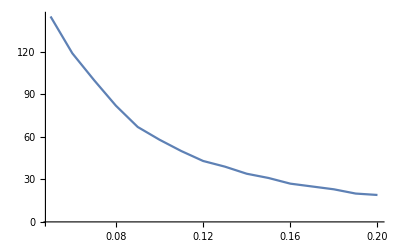

```mathematica
(*Доверительный уровень*)
δ=0.1;
(*Вводим данные, согласно условию*)
(*Невозрастающая последовательность собственных чисел ковариационного оператора*)
λ[k_]:=1/(π^2 k^2);
(*Соотвтетствующие собственным числам собственные функции*)
(*Subscript[Κψ, k]=Subscript[λ, k] Subscript[ψ, k]  k=1,2,...*)
ψ[k_, t_]:=√2 Cos[π k t];
(*Задем след ковариационного оператора*)
Λ=∑_(k=1)^(+∞) λ[k];
(*Количество выборок случайных величин*)
NS=100;
(*Объем каждой выюорки*)
NCS=300;
(*Задаем матрицу случайных величин - выборки*)
(*Случайные величины в строке приналежат к одной выборке*)
MS=Table[RandomVariate[NormalDistribution[0,1]],{i,1,NCS} ,{j,1,NS}];
(*Построить график зависимости ϵ↦n^prob(ϵ,δ)*)
(*Начальное значение порога ошибки*)
start = 0.2;
(*Конечное значение порога ошибки*)
end = 0.05;
(*Шаг изменения порога ошибки*)
step=0.01;
(*Список для хранения сложности
аппроксимации по вероятности от заданного порога ошибки при фиксированом доверительном уровне*)
navgs=List[];
(*Список для хранения порогов ошибки*)
errors=List[];

For[ϵ=start, ϵ≥ end, ϵ=ϵ-step,
(*Начальные значения частичных сумм*)
PartAmount = Table[∑_(k=1)^NCS λ[k]*(MS[[k,i]])^2,{i,1,NS}];
AppendTo[errors,ϵ];
(*Начальное значение вероятности равно 1*)
P=1;
(*Задаем начальное значение для n*)
n=0;
(*Пока вероятность больше заданой доверительной ошибки*)
While[P>δ,
(*Количество успехов*)
SC=0;
(*Цикл по всем выборкам*)
For[i=1, i≤NS,  i++,
(*Если условие выполено, то увеличиваем количество успехов*)
If[PartAmount[[i]]>  ϵ^2*Λ,SC=SC+1; ];
(*Уменьшаем частичную сумму*)
PartAmount[[i]]= PartAmount[[i]]-λ[n+1]*(MS[[n+1,i]])^2;
 ];(*Конец цикла по выборкам*)
(*Увеличиваем n*)
n=n+1;
(*Считаем вероятность P = (количество успехов)/(количество выборок)*)
P=SC/NS;
];(*Конец цикла пока*)
AppendTo[navgs, n];
];(*Цикл по порогам ошибки*)
Print[errors]
Print[navgs]
(*Строим график зависимости сложности
аппроксимации по вероятности от заданного порога ошибки при фиксированом доверительном уровне*)
Print[ListLinePlot[Table[{errors[[i]],navgs[[i]]},{i,1,Length[navgs]}]]];
```